## Parameters

1. DE with w=-1 ~ LCDM

w=-1;
Ω_DE0=0.734;
Ω_k0=0;
Ω_m0=0.1334/(0.71^2);
Ω_r0=8.09*10^-5;
H_0=71/300000;

## DE & LCDM & sCDM

Hubble distance

```mathematica
w=-1;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
Subscript[H, 0]=71/300000;
H[a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+w)));
Subscript[d, H]=1/H[a]
1/NIntegrate[1/(x^2 H[x]),{x,0,a}]
```

300000/(71 √(0.734+0.0000809/a^4+0.26463/a^3))

Growth function

```mathematica
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.5;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
Subscript[H, 0]=71/300000;
Subscript[Ω, m0,s]=1;Subscript[Ω, r0,s]=8.09*10^-5;Subscript[H, 0]=71/300000;
Subscript[H, s][a_]:=Subscript[H, 0] √(Subscript[Ω, m0,s] a^-3+Subscript[Ω, r0,s] a^-4);
Subscript[H, L][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 1])))
Subscript[H, 2][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 2])))
Subscript[d, H,L][a]=1/(Subscript[H, L][a]);Subscript[d, H,2][a]=1/(Subscript[H, 2][a]);
kL[a_]=Subscript[H, L][a];Subscript[kL, 2][a_]=Subscript[H, 2][a];Subscript[k, s][a_]=Subscript[H, s][a];
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k==Subscript[H, 2][Subscript[a, 2]],Subscript[a, 2]];*)
Subscript[Growth, s][a_]:= 5/2 Subscript[Ω, m0,s] (Subscript[H, s][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, s][x])/Subscript[H, 0])^3),{x,0,a}];
GrowthL[a_]:= 5/2 Subscript[Ω, m0] (Subscript[H, L][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, L][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 2][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 2][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 2][x])/Subscript[H, 0])^3),{x,0,a}];
(*k~a*)
LogPlot[{kL[a],Subscript[kDE, 2][a],Subscript[k, s][a]},{a,10^-3,1}];
(*eg*)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {-9,0}];
(*Growth~a*)
Plot[{GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[Growth, s][a]},{a,0,1},PlotStyle->{Red,Green,Black},AxesLabel-> {a,"D_+(a)"}];
(*Growth with respect to 1+z*)
xyz[mn_]:=GrowthL[1/mn];rst[mn_]:=Subscript[GrowthDE, 2][1/mn];uvw[mn_]:=Subscript[Growth, s][1/mn];
LogLogPlot[{(mn)xyz[mn],(mn)rst[mn]},{mn,0.1,100},AxesLabel-> {"1+z","D_+(z)(1+z)"}];
(*The Q factor*)
(*DataList*)
PowerS=Import["E:\\KuaiPan\\MA_Lei\\PSLCDM.dat"];
PowerS[[1,1]]
Solve[PowerS[[1,1]]==Subscript[H, L][Subscript[a, L]],Subscript[a, L],Reals]
NSolve[PowerS[[1,1]]==Subscript[H, L][Subscript[a, L]],Subscript[a, L],Reals]
solL:=Solve[PowerS[[i,1]]==Subscript[H, L][Subscript[a, L]] && Subscript[a, L]>0,Subscript[a, L],Reals]
aokTabL=Table[Subscript[a, L]/.solL,{i,1,10}];
solDE2:=Solve[PowerS[[i,1]]==Subscript[H, L][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals]
aokTabDE2=Table[Subscript[a, 2]/.solDE2,{i,1,10}]
Qfactor=Table[{PowerS[[i,1]],((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,Length[PowerS]}]
ListLogLinearPlot[Qfactor,Joined->True, AxesLabel-> {k,Q},PlotRange->Full]
PowerSDE2=Table[{PowerS[[i,1]],((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])PowerS[[i,2]]},{i,1,Length[PowerS]}]
ListLogLinearPlot[PowerSDE2,Joined->True, AxesLabel-> {k,PowerSpectrum},PlotRange->Full]
(*Table[NSolve[PowerS[[i,1]]==Subscript[H, 2][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals],{i,1,Length[PowerS]}]*)
```

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

0.00100027

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a_L→-0.00030571},{a_L→0.24916}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a_L→-0.00030571},{a_L→0.24916}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

{{0.24916},{0.248592},{0.248029},{0.247468},{0.24691},{0.246357},{0.245805},{0.245258},{0.244713},{0.24417}}

Part::partw: Part 11 of {{0.24916}, {0.248592}, {0.248029}, {0.247468}, {0.24691}, {0.246357}, {0.245805}, {0.245258}, {0.244713}, {0.24417}} does not exist.

NIntegrate::nlim: x = {{0.24916}, {0.248592}, {0.248029}, {0.247468}, {0.24691}, {0.246357}, {0.245805}, {0.245258}, {0.244713}, {0.24417}} is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

Part::partw: Part 11 of {{0.24916}, {0.248592}, {0.248029}, {0.247468}, {0.24691}, {0.246357}, {0.245805}, {0.245258}, {0.244713}, {0.24417}} does not exist.

Part::partw: Part 12 of {{0.24916}, {0.248592}, {0.248029}, {0.247468}, {0.24691}, {0.246357}, {0.245805}, {0.245258}, {0.244713}, {0.24417}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NIntegrate::nlim: x = {{0.24916}, {0.248592}, {0.248029}, {0.247468}, {0.24691}, {0.246357}, {0.245805}, {0.245258}, {0.244713}, {0.24417}} is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{0.00100027,0.761103},«2737»,{5.70289,{{(0.590468 NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,{{0.24916},{0.248592},«6»,{0.244713},{0.24417}}}])/NIntegrate[1/(x^3 (H_2[x]/H_0)^3),{x,0,{{0.24916},{0.248592},«6»,{0.244713},{0.24417}}}]},«8»,{(«19» «10»[«1»])/NIntegrate[«1»]}}}}

NIntegrate::nlim: x = {{0.24916}, {0.248592}, {0.248029}, {0.247468}, {0.24691}, {0.246357}, {0.245805}, {0.245258}, {0.244713}, {0.24417}} is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

## Write Data to files.

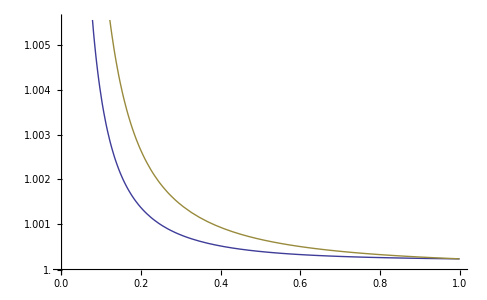

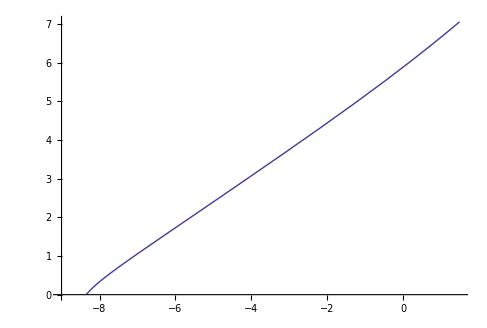

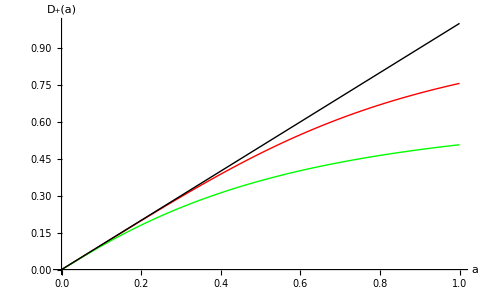

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained 41.459  + 55.5417\ ⅈ
 and 38.5744 for the integral and error estimates.

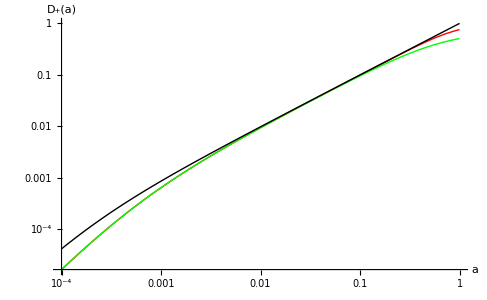

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

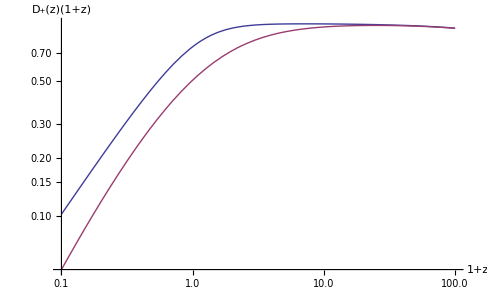

```mathematica
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.5;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
h=0.71;
Subscript[H, 0]=(100 h)/300000;
Subscript[Ω, m0,s]=1;Subscript[Ω, r0,s]=8.09*10^-5;
Subscript[H, s][a_]:=Subscript[H, 0] √(Subscript[Ω, m0,s] a^-3+Subscript[Ω, r0,s] a^-4);
Subscript[H, L][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 1])))
Subscript[H, 2][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 2])))
Subscript[d, H,L][a]=1/(Subscript[H, L][a]);Subscript[d, H,2][a]=1/(Subscript[H, 2][a]);
kL[a_]=Subscript[H, L][a];Subscript[kL, 2][a_]=Subscript[H, 2][a];Subscript[k, s][a_]=Subscript[H, s][a];
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k==Subscript[H, 2][Subscript[a, 2]],Subscript[a, 2]];*)
Subscript[Growth, s][a_]:= 5/2 Subscript[Ω, m0,s] (Subscript[H, s][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, s][x])/Subscript[H, 0])^3),{x,0,a}];
GrowthL[a_]:= 5/2 Subscript[Ω, m0] (Subscript[H, L][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, L][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthDE, 2][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 2][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 2][x])/Subscript[H, 0])^3),{x,0,a}];
(*k~a*)
LogPlot[{kL[a],Subscript[kDE, 2][a],Subscript[k, s][a]},{a,10^-3,1}]
(*eg*)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {-9,0}]
(*Growth~a*)
Plot[{GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[Growth, s][a]},{a,0,1},PlotStyle->{Red,Green,Black},AxesLabel-> {a,"D_+(a)"}]
LogLogPlot[{GrowthL[a],Subscript[GrowthDE, 2][a],Subscript[Growth, s][a]},{a,10^-4,1},PlotStyle->{Red,Green,Black},AxesLabel-> {a,"D_+(a)"}]
(*Growth with respect to 1+z*)
xyz[mn_]:=GrowthL[1/mn];rst[mn_]:=Subscript[GrowthDE, 2][1/mn];uvw[mn_]:=Subscript[Growth, s][1/mn];
LogLogPlot[{(mn)xyz[mn],(mn)rst[mn]},{mn,0.1,100},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
(*The Q factor*)
(*DataList*)
```

```mathematica
PowerS=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PowerspectrumLCDMdataLongrange.dat"];
PowerS[[1,1]]
leth=Length[PowerS]
Solve[PowerS[[1,1]]==Subscript[H, L][Subscript[a, L]],Subscript[a, L],Reals]
NSolve[PowerS[[1,1]]==Subscript[H, L][Subscript[a, L]],Subscript[a, L],Reals]
```

0.0000147064

4083

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a_L→-0.712879},{a_L→-0.00030571}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a_L→-0.712879},{a_L→-0.00030571}}

```mathematica
(*Test the Hubble equation*)
Subscript[H, L][1]
Subscript[H, L][0.01]/h
Subscript[H, L][0.001]/h
Subscript[H, L][0.0001]/h
Subscript[H, L][0.00001]/h
Subscript[H, L][0.000001]/h
```

0.000236514

0.174076

6.19615

345.387

30467.9

3.00305×10^6

```mathematica
aokTabL=Table[Subscript[a, L]/.NSolve[PowerS[[i,1]]==Subscript[H, L][Subscript[a, L]] && Subscript[a, L]>0,Subscript[a, L],Reals],{i,1,leth}];
aokTabDE2=Table[Subscript[a, 2]/.NSolve[PowerS[[i,1]]==Subscript[H, L][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals],{i,1,leth}];
aokTabL[[1740]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

{0.106405}

```mathematica
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\aokTabL_Adiab.xls",aokTabL,"XLS"]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\aokTabDE2_Adiab.xls",aokTabDE2,"XLS"]
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\aokTabL_Adiab.xls

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\aokTabDE2_Adiab.xls

```mathematica
Qfactor=Table[{PowerS[[i,1]],((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]])},{i,1,leth}]
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\QfactorDE2vsL_Adiab.xls",Qfactor,"XLS"]
```

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

{{0.0000147064,(0.670459 √(0.734+0.0000809/a^4+0.26463/a^3) NIntegrate[1/(x^3 (H_L[x]/H_0)^3),{x,0,a}])/(√(0.0000809/a^4+0.26463/a^3+0.734/a^1.5) NIntegrate[1/(x^3 (H_2[x]/H_0)^3),{x,0,a}])},«4081»,{5.70289,0.670474}}

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\QfactorDE2vsL_Adiab.xls

```mathematica
PowerSDE2=Table[{PowerS[[i,1]]/h,(((Subscript[GrowthDE, 2][1])/(Subscript[GrowthDE, 2][aokTabDE2[[i]][[1]]]))/(GrowthL[1]/GrowthL[aokTabL[[i]][[1]]]))^2 PowerS[[i,2]] h^3 (PowerS[[i,1]]/h)^4},{i,1,leth}];
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PowerSDE2_Adiab.xls",PowerSDE2,"XLS"]
```

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\PowerSDE2_Adiab.xls

```mathematica
PowerSS=Table[{PowerS[[i,1]]/h,PowerS[[i,2]]  h^3 (PowerS[[i,1]]/h)^4},{i,1,leth}];
Export["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PowerSScale_Adiab.xls",PowerSS,"XLS"]
PowerSScale=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PowerSScale_Adiab.xls"];
PowDeHalf=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PowerSDE2_Adiab.xls"];
QfDeVsL=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\QfactorDE2vsL_Adiab.xls"];
ListLogLogPlot[{PowerSScale,PowDeHalf},Joined->True, AxesLabel-> {k,PowerSpectrum},PlotRange->Automatic]
ListLogLogPlot[QfDeVsL,Joined->True, AxesLabel-> {k,Q},PlotRange->Full]
ListLogLinearPlot[QfDeVsL,Joined->True, AxesLabel-> {k,Q},PlotRange->Full]
(*Table[NSolve[PowerS[[i,1]]==Subscript[H, 2][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals],{i,1,Length[PowerS]}]*)
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica\PowerSScale_Adiab.xls

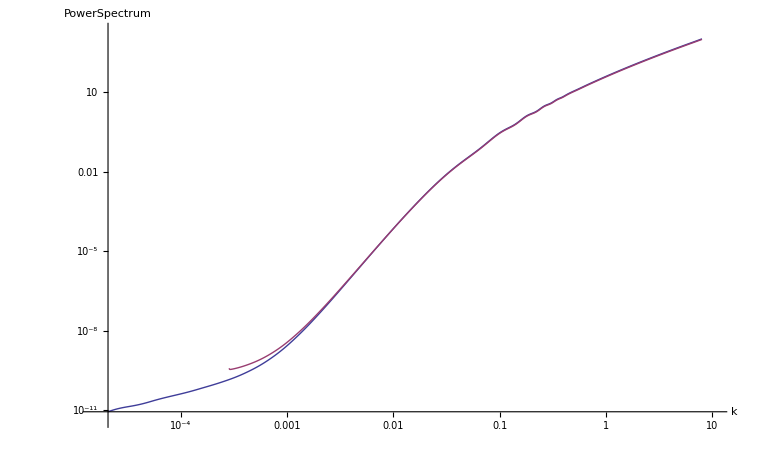

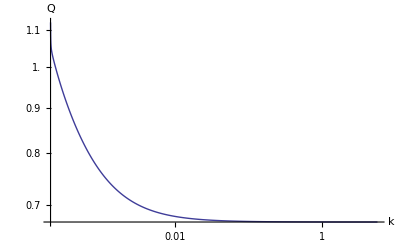

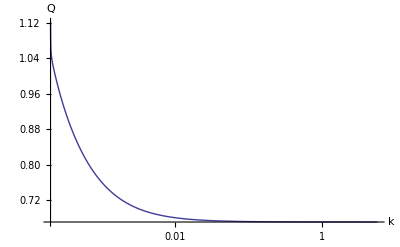

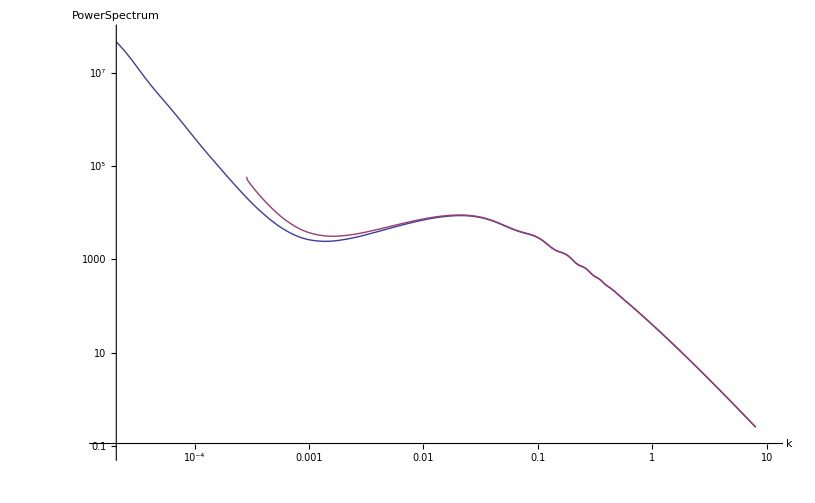

-Graphics-

-Graphics-

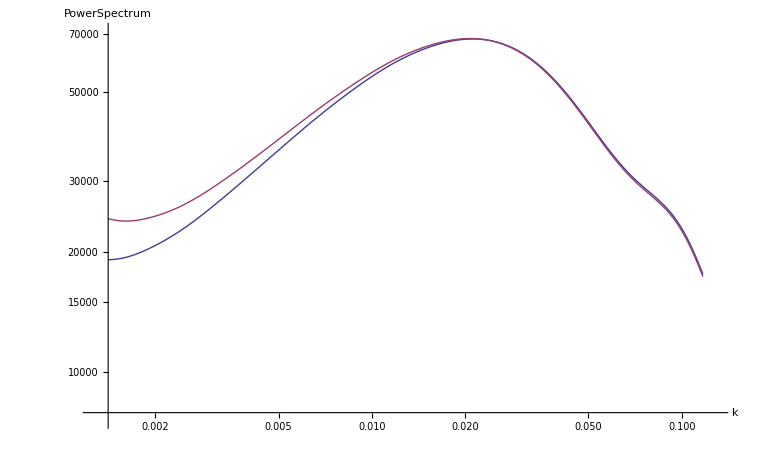

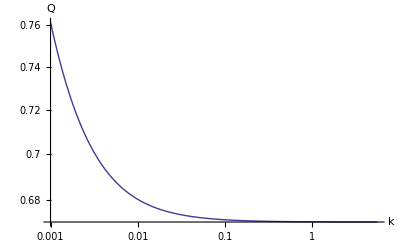

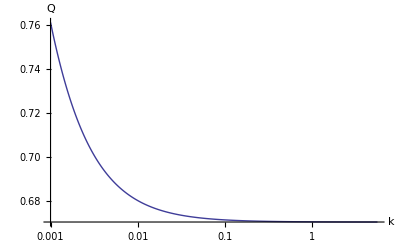

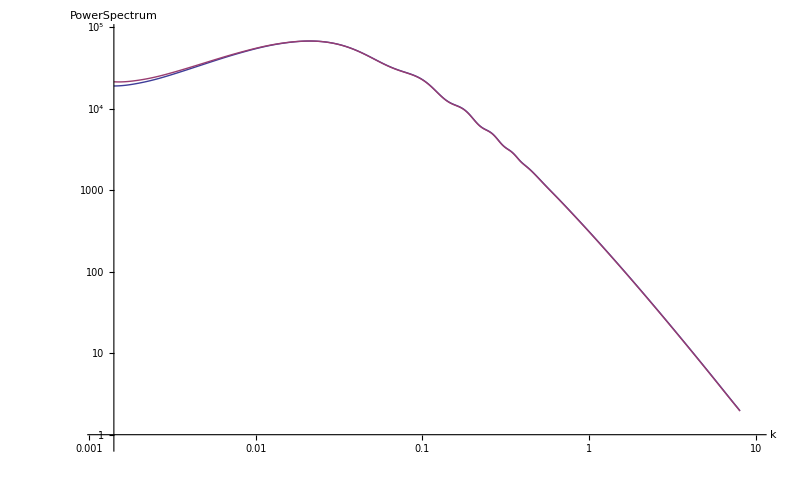

-Graphics-

-Graphics-

## Draft

Use particle horizon

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

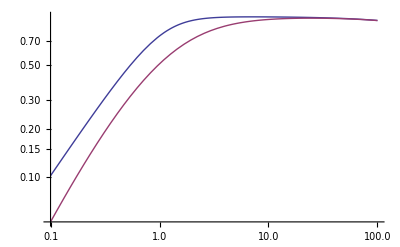

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.714939}. NIntegrate obtained 183.512  + 36.182\ ⅈ
 and 146.651 for the integral and error estimates.

```mathematica
Subscript[w, 1]=-1;
Subscript[w, 2]=-0.5;
Subscript[Ω, DE0]=0.734;
Subscript[Ω, k0]=0;
Subscript[Ω, m0]=0.1334/(0.71^2);
Subscript[Ω, r0]=8.09*10^-5;
Subscript[H, 0]=71/300000;
Subscript[H, 1][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 1])))
Subscript[H, 2][a_]:=Subscript[H, 0] √(Subscript[Ω, m0] a^-3+Subscript[Ω, r0] a^-4+Subscript[Ω, DE0] a^(-3(1+Subscript[w, 2])))
Subscript[d, H,1][a]=1/(Subscript[H, 1][a]);Subscript[d, H,2][a]=1/(Subscript[H, 2][a]);

Subscript[kL, 1][a_]=1/NIntegrate[1/(x^2 Subscript[H, 1][x]),{x,0,a}];Subscript[kL, 2][a_]=1/NIntegrate[1/(x^2 Subscript[H, 2][x]),{x,0,a}];
Subscript[GrowthL, 1][a_]:= 5/2 Subscript[Ω, m0] (Subscript[H, 1][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 1][x])/Subscript[H, 0])^3),{x,0,a}];
Subscript[GrowthL, 2][a_]:=5/2 Subscript[Ω, m0] (Subscript[H, 2][a])/Subscript[H, 0]  NIntegrate[1/(x^3((Subscript[H, 2][x])/Subscript[H, 0])^3),{x,0,a}];
(*Add some test*)
xyz[mn_]:=Subscript[GrowthL, 1][1/mn];rst[mn_]=Subscript[GrowthL, 2][1/mn];
LogLogPlot[{(mn) xyz[mn],(mn) rst[mn]},{mn,0.1,100}]

LogPlot[{Subscript[kL, 1][a],Subscript[kL, 2][a]},{a,10^-3,1}];
LogLogPlot[{Subscript[GrowthL, 1][a],Subscript[GrowthL, 2][a]},{a,10^-3,1}];
Plot[{(Subscript[GrowthL, 1][1])/(Subscript[GrowthL, 1][a]),(Subscript[GrowthL, 2][1])/(Subscript[GrowthL, 2][a])},{a,10^-3,1}];
```

## Data

datalist

```mathematica
PowerS=Import["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\PSLCDM.dat"];
Table[PowerS[[i,2]],{i,1,Length[PowerS]}]
```

{6834.63,6834.85,6835.17,6835.6,6836.14,6836.78,6837.52,6838.36,6839.31,6840.35,6841.49,6842.73,6844.07,6845.51,6847.04,6848.66,6848.66,6850.49,6852.43,6854.48,6856.62,6858.87,6861.22,6863.67,6866.21,6868.86,6871.6,6874.43,6877.36,6880.38,6883.49,6886.7,6889.99,6893.37,6896.84,6900.4,6904.04,6908.02,6912.09,6916.26,6920.51,6924.86,6929.3,6933.83,6938.44,6943.14,6947.92,6952.79,6957.73,6962.76,6967.87,6973.06,6978.32,6983.66,6989.07,6994.56,7000.12,7006.13,7012.21,7018.37,7024.61,7030.92,7037.3,7043.76,7050.28,7056.86,7063.51,7070.22,7076.99,7083.82,7090.71,7097.65,7104.65,7111.7,7118.79,7125.94,7133.13,7133.13,7140.85,7148.61,7156.43,7164.29,7172.2,7180.15,7188.14,7196.18,7204.25,7212.36,7220.51,7228.7,7236.92,7245.17,7253.46,7261.77,7270.12,7278.49,7286.9,7295.32,7295.32,7304.34,7313.38,7322.46,7331.56,7340.69,7349.84,7359.03,7368.24,7377.49,7386.76,7396.06,7405.39,7414.74,7424.13,7433.55,7443,7452.47,7461.98,7471.52,7481.08,7491.32,7501.59,7511.9,7522.24,7532.62,7543.02,7553.46,7563.94,7574.44,7584.98,7595.55,7606.15,7616.79,7627.45,7638.15,7648.88,7659.64,7670.43,7681.25,7692.1,7703.71,7715.35,7727.02,7738.73,7750.48,7762.25,7774.06,7785.91,7797.78,7809.69,7821.63,7833.6,7845.6,7857.64,7869.71,7881.8,7893.93,7906.09,7918.29,7930.51,7943.58,7956.69,7969.83,7983,7996.21,8009.45,8022.73,8036.04,8049.38,8062.75,8076.15,8089.59,8103.05,8116.55,8130.08,8143.64,8157.23,8170.84,8184.49,8198.17,8212.79,8227.45,8242.13,8256.85,8271.6,8286.38,8301.2,8316.04,8330.91,8345.81,8360.74,8375.7,8390.69,8405.7,8420.74,8435.81,8450.9,8466.02,8481.17,8496.34,8496.34,8512.56,8528.8,8545.06,8561.36,8577.68,8594.03,8610.4,8626.79,8643.21,8659.66,8676.12,8692.61,8709.12,8725.66,8742.21,8758.78,8775.37,8791.99,8808.62,8825.26,8825.26,8843.04,8860.84,8878.66,8896.49,8914.35,8932.21,8950.09,8967.99,8985.89,9003.81,9021.74,9039.68,9057.63,9075.59,9093.56,9111.53,9129.51,9147.49,9165.48,9183.47,9202.66,9221.86,9241.05,9260.25,9279.45,9298.65,9317.85,9337.05,9356.25,9375.45,9394.65,9413.84,9433.03,9452.22,9471.41,9490.6,9509.78,9528.95,9548.12,9567.29,9587.73,9608.17,9628.6,9649.02,9669.44,9689.85,9710.26,9730.66,9751.05,9771.44,9791.82,9812.19,9832.56,9852.92,9873.27,9893.62,9913.96,9934.3,9954.63,9974.95,9974.95,9996.62,10018.3,10039.9,10061.6,10083.2,10104.9,10126.5,10148.1,10169.7,10191.3,10212.9,10234.5,10256,10277.6,10299.1,10320.7,10342.2,10363.7,10385.2,10406.7,10429.6,10452.5,10475.4,10498.3,10521.2,10544.1,10566.9,10589.7,10612.6,10635.4,10658.2,10680.9,10703.7,10726.5,10749.2,10771.9,10794.6,10817.3,10840,10862.7,10886.8,10911,10935.1,10959.2,10983.3,11007.4,11031.5,11055.5,11079.6,11103.6,11127.6,11151.6,11175.5,11199.5,11223.4,11247.3,11271.2,11295,11318.9,11342.7,11368.1,11393.5,11418.9,11444.2,11469.5,11494.8,11520.1,11545.3,11570.6,11595.8,11620.9,11646.1,11671.2,11696.3,11721.4,11746.5,11771.5,11796.6,11821.6,11846.5,11873.1,11899.7,11926.3,11952.8,11979.3,12005.8,12032.3,12058.7,12085.1,12111.5,12137.8,12164.1,12190.4,12216.7,12242.9,12269.1,12295.3,12321.4,12347.5,12373.6,12401.4,12429.2,12457,12484.7,12512.3,12540,12567.6,12595.2,12622.7,12650.2,12677.7,12705.2,12732.6,12760,12787.3,12814.6,12841.9,12869.2,12896.4,12923.6,12923.6,12952.6,12981.5,13010.4,13039.3,13068.1,13096.9,13125.7,13154.4,13183.1,13211.7,13240.3,13268.9,13297.4,13325.9,13354.3,13382.7,13411.1,13439.4,13467.7,13495.9,13526,13556.1,13586.1,13616,13645.9,13675.8,13705.6,13735.3,13765,13794.7,13824.3,13853.9,13883.4,13912.9,13942.3,13971.7,14001,14030.2,14059.5,14088.6,14119.7,14150.7,14181.7,14212.5,14243.4,14274.2,14304.9,14335.5,14366.1,14396.7,14427.2,14457.6,14487.9,14518.2,14548.5,14578.7,14608.8,14638.9,14668.9,14698.8,14730.7,14762.5,14794.3,14825.9,14857.5,14889.1,14920.6,14952,14983.3,15014.5,15045.7,15076.9,15107.9,15138.9,15169.8,15200.6,15231.4,15262.1,15292.8,15323.3,15323.3,15355.8,15388.3,15420.7,15452.9,15485.2,15517.3,15549.3,15581.3,15613.2,15645,15676.7,15708.4,15740,15771.5,15802.9,15834.2,15865.5,15896.6,15927.7,15958.8,15991.8,16024.7,16057.5,16090.3,16122.9,16155.5,16188,16220.3,16252.6,16284.9,16317,16349,16381,16412.8,16444.6,16476.3,16507.9,16539.5,16570.9,16602.2,16635.6,16668.9,16702,16735.1,16768.1,16801,16833.7,16866.4,16899,16931.6,16964,16996.3,17028.6,17060.7,17092.8,17124.8,17156.7,17188.5,17220.2,17251.8,17251.8,17285.5,17319.1,17352.5,17385.9,17419.2,17452.4,17485.5,17518.5,17551.4,17584.2,17616.9,17649.6,17682.1,17714.6,17747,17779.3,17811.5,17843.6,17875.7,17907.6,17941.6,17975.6,18009.4,18043.1,18076.7,18110.2,18143.7,18177,18210.3,18243.4,18276.5,18309.4,18342.2,18375,18407.6,18440.2,18472.6,18505,18537.2,18569.4,18603.6,18637.6,18671.6,18705.4,18739.1,18772.7,18806.2,18839.6,18872.8,18905.9,18938.9,18971.8,19004.6,19037.3,19069.8,19102.2,19134.5,19166.7,19198.7,19230.7,19264.6,19298.4,19332.1,19365.6,19399,19432.2,19465.4,19498.3,19531.2,19563.9,19596.4,19628.9,19661.2,19693.3,19725.3,19757.2,19788.9,19820.5,19852,19883.3,19883.3,19916.5,19949.6,19982.6,20015.4,20048,20080.4,20112.8,20144.9,20176.9,20208.7,20240.4,20271.9,20303.3,20334.5,20365.5,20396.4,20427.1,20457.7,20488.1,20518.3,20518.3,20550.4,20582.4,20614.1,20645.7,20677.1,20708.3,20739.3,20770.2,20800.8,20831.3,20861.7,20891.8,20921.8,20951.6,20981.2,21010.6,21039.9,21069,21097.9,21126.7,21126.7,21157.2,21187.5,21217.5,21247.4,21277.1,21306.6,21335.9,21365.1,21394,21422.7,21451.2,21479.6,21507.8,21535.7,21563.5,21591.1,21618.5,21645.7,21672.8,21699.6,21699.6,21728.1,21756.3,21784.3,21812.2,21839.8,21867.2,21894.4,21921.4,21948.2,21974.8,22001.2,22027.4,22053.4,22079.2,22104.8,22130.2,22155.5,22180.5,22205.3,22230,22256.1,22282,22307.6,22333.1,22358.3,22383.4,22408.2,22432.8,22457.3,22481.5,22505.6,22529.4,22553,22576.5,22599.8,22622.9,22645.8,22668.5,22691,22713.4,22737,22760.5,22783.7,22806.8,22829.6,22852.3,22874.7,22897,22919.1,22941,22962.7,22984.2,23005.5,23026.6,23047.6,23068.3,23088.9,23109.3,23129.5,23149.6,23170.8,23191.7,23212.5,23233.1,23253.5,23273.6,23293.6,23313.4,23333,23352.3,23371.5,23390.5,23409.2,23427.8,23446.1,23464.3,23482.2,23500,23517.5,23534.9,23534.9,23553.2,23571.2,23589,23606.6,23624,23641.1,23658,23674.7,23691.2,23707.4,23723.4,23739.2,23754.8,23770.1,23785.2,23800.1,23814.8,23829.2,23843.5,23857.5,23872.2,23886.6,23900.8,23914.8,23928.5,23941.9,23955.2,23968.1,23980.9,23993.4,24005.6,24017.6,24029.4,24040.9,24052.2,24063.2,24074,24084.6,24094.9,24105,24105,24115.5,24125.8,24135.8,24145.5,24155,24164.2,24173.1,24181.8,24190.2,24198.4,24206.3,24213.9,24221.3,24228.5,24235.4,24242,24248.4,24254.6,24260.5,24266.2,24272,24277.5,24282.7,24287.6,24292.3,24296.8,24300.9,24304.8,24308.4,24311.8,24314.9,24317.7,24320.3,24322.6,24324.7,24326.6,24328.1,24329.5,24330.5,24331.4,24331.4,24332,24332.4,24332.4,24332.3,24331.8,24331.1,24330.1,24328.8,24327.3,24325.5,24323.4,24321.1,24318.5,24315.6,24312.5,24309.2,24305.6,24301.7,24297.6,24293.2,24293.2,24288.3,24283.1,24277.6,24271.8,24265.8,24259.4,24252.8,24245.9,24238.8,24231.4,24223.7,24215.8,24207.6,24199.1,24190.4,24181.4,24172.1,24162.6,24152.9,24142.9,24142.9,24132,24120.7,24109.2,24097.4,24085.4,24073.1,24060.5,24047.6,24034.5,24021.1,24007.4,23993.5,23979.3,23964.9,23950.2,23935.3,23920.1,23904.7,23889,23873.1,23873.1,23855.9,23838.4,23820.6,23802.6,23784.3,23765.7,23746.9,23727.9,23708.6,23689,23669.2,23649.2,23628.9,23608.4,23587.7,23566.7,23545.5,23524.1,23502.5,23480.6,23480.6,23457.1,23433.3,23409.2,23385,23360.5,23335.7,23310.8,23285.6,23260.2,23234.6,23208.7,23182.6,23156.4,23129.9,23103.2,23076.2,23049.1,23021.8,22994.3,22966.6,22966.6,22936.8,22906.8,22876.6,22846.2,22815.5,22784.7,22753.6,22722.4,22690.9,22659.3,22627.4,22595.4,22563.2,22530.8,22498.2,22465.4,22432.4,22399.3,22366,22332.5,22296.7,22260.6,22224.3,22187.9,22151.3,22114.5,22077.5,22040.4,22003.1,21965.6,21928,21890.3,21852.3,21814.3,21776.1,21737.7,21699.2,21660.6,21621.8,21582.9,21582.9,21541.3,21499.6,21457.7,21415.6,21373.5,21331.2,21288.8,21246.3,21203.6,21160.9,21118,21075,21031.9,20988.8,20945.5,20902.1,20858.7,20815.2,20771.5,20727.8,20727.8,20681.1,20634.4,20587.5,20540.5,20493.5,20446.5,20399.3,20352.1,20304.8,20257.5,20210.1,20162.7,20115.2,20067.7,20020.2,19972.6,19925,19877.3,19829.6,19782,19731.1,19680.1,19629.2,19578.3,19527.3,19476.4,19425.4,19374.5,19323.6,19272.7,19221.8,19170.9,19120,19069.2,19018.4,18967.6,18916.9,18866.2,18815.6,18765,18711,18657.2,18603.4,18549.7,18496,18442.4,18388.9,18335.5,18282.2,18228.9,18175.7,18122.7,18069.7,18016.8,17964,17911.4,17858.8,17806.3,17754,17701.8,17646.2,17590.7,17535.4,17480.3,17425.3,17370.4,17315.7,17261.1,17206.7,17152.5,17098.5,17044.6,16990.8,16937.3,16883.9,16830.7,16777.7,16724.9,16672.3,16619.8,16619.8,16564.1,16508.6,16453.3,16398.2,16343.4,16288.8,16234.5,16180.3,16126.4,16072.8,16019.4,15966.2,15913.3,15860.6,15808.2,15756,15704,15652.4,15600.9,15549.8,15495.5,15441.4,15387.7,15334.3,15281.2,15228.4,15175.9,15123.7,15071.8,15020.2,14968.9,14917.9,14867.2,14816.8,14766.8,14717.1,14667.6,14618.5,14569.8,14521.3,14469.9,14419,14368.3,14318.1,14268.2,14218.7,14169.5,14120.7,14072.3,14024.2,13976.5,13929.1,13882.1,13835.5,13789.2,13743.3,13697.7,13652.5,13607.7,13563.2,13563.2,13516.1,13469.4,13423.2,13377.3,13331.9,13286.8,13242.2,13197.9,13154.1,13110.6,13067.5,13024.9,12982.6,12940.7,12899.2,12858.1,12817.4,12777,12737.1,12697.5,12697.5,12655.7,12614.4,12573.4,12532.9,12492.9,12453.2,12414,12375.1,12336.7,12298.7,12261.1,12223.8,12187,12150.6,12114.6,12078.9,12043.6,12008.8,11974.2,11940.1,11940.1,11904.1,11868.5,11833.3,11798.5,11764.1,11730.2,11696.6,11663.4,11630.6,11598.2,11566.1,11534.4,11503.1,11472.2,11441.6,11411.4,11381.5,11352,11322.8,11293.9,11263.5,11233.5,11203.8,11174.5,11145.6,11117,11088.7,11060.8,11033.2,11005.9,10979,10952.4,10926,10900,10874.3,10848.9,10823.7,10798.9,10774.3,10749.9,10724.2,10698.9,10673.8,10648.9,10624.4,10600.1,10576,10552.2,10528.7,10505.3,10482.2,10459.3,10436.7,10414.2,10391.9,10369.8,10347.9,10326.2,10304.7,10283.3,10283.3,10260.6,10238.1,10215.8,10193.7,10171.6,10149.8,10128,10106.4,10084.9,10063.5,10042.3,10021.1,9999.99,9978.98,9958.05,9937.19,9916.39,9895.64,9874.93,9854.27,9854.27,9832.26,9810.29,9788.34,9766.4,9744.48,9722.56,9700.64,9678.72,9656.78,9634.82,9612.83,9590.81,9568.76,9546.65,9524.5,9502.29,9480.02,9457.67,9435.25,9412.75,9412.75,9388.64,9364.43,9340.12,9315.69,9291.14,9266.48,9241.7,9216.78,9191.74,9166.57,9141.26,9115.81,9090.22,9064.48,9038.59,9012.55,8986.35,8959.99,8933.46,8906.77,8878.1,8849.25,8820.19,8790.95,8761.52,8731.89,8702.08,8672.08,8641.89,8611.51,8580.95,8550.21,8519.28,8488.17,8456.88,8425.41,8393.76,8361.93,8329.92,8297.74,8297.74,8263.21,8228.49,8193.59,8158.5,8123.24,8087.81,8052.22,8016.47,7980.57,7944.52,7908.34,7872.02,7835.58,7799.02,7762.34,7725.56,7688.67,7651.69,7614.62,7577.47,7577.47,7537.75,7497.95,7458.09,7418.16,7378.19,7338.18,7298.14,7258.08,7218.02,7177.95,7137.89,7097.86,7057.85,7017.88,6977.97,6938.11,6898.32,6858.61,6818.99,6779.47,6737.43,6695.52,6653.76,6612.15,6570.7,6529.43,6488.34,6447.44,6406.74,6366.26,6326,6285.97,6246.18,6206.65,6167.37,6128.37,6089.65,6051.23,6013.1,5975.29,5935.3,5895.68,5856.44,5817.59,5779.12,5741.04,5703.37,5666.09,5629.23,5592.79,5556.76,5521.16,5486,5451.27,5416.99,5383.15,5349.77,5316.85,5284.4,5252.42,5218.82,5185.77,5153.26,5121.28,5089.84,5058.94,5028.57,4998.72,4969.41,4940.62,4912.36,4884.63,4857.41,4830.72,4804.54,4778.88,4753.74,4729.11,4704.99,4681.38,4656.75,4632.69,4609.19,4586.24,4563.83,4541.95,4520.59,4499.74,4479.39,4459.54,4440.17,4421.26,4402.83,4384.84,4367.3,4350.19,4333.51,4317.25,4301.39,4285.92,4285.92,4269.85,4254.2,4238.96,4224.11,4209.65,4195.54,4181.79,4168.37,4155.27,4142.47,4129.96,4117.72,4105.74,4094,4082.49,4071.19,4060.09,4049.17,4038.42,4027.82,4027.82,4016.66,4005.64,3994.75,3983.97,3973.28,3962.68,3952.14,3941.65,3931.2,3920.78,3910.36,3899.93,3889.48,3878.99,3868.45,3857.84,3847.16,3836.37,3825.47,3814.45,3802.54,3790.46,3778.22,3765.8,3753.2,3740.41,3727.44,3714.28,3700.91,3687.34,3673.57,3659.58,3645.38,3630.95,3616.3,3601.42,3586.3,3570.94,3555.33,3539.48,3522.28,3504.81,3487.07,3469.07,3450.82,3432.33,3413.61,3394.68,3375.54,3356.2,3336.68,3316.98,3297.12,3277.1,3256.94,3236.64,3216.22,3195.69,3175.05,3154.32,3154.32,3132.12,3109.84,3087.5,3065.11,3042.7,3020.28,2997.87,2975.48,2953.14,2930.85,2908.63,2886.51,2864.49,2842.6,2820.84,2799.25,2777.83,2756.61,2735.59,2714.79,2692.88,2671.24,2649.89,2628.84,2608.09,2587.66,2567.53,2547.73,2528.27,2509.13,2490.35,2471.91,2453.83,2436.12,2418.78,2401.81,2385.24,2369.05,2353.26,2337.88,2337.88,2321.92,2306.43,2291.38,2276.78,2262.61,2248.87,2235.53,2222.61,2210.08,2197.93,2186.16,2174.76,2163.72,2153.03,2142.67,2132.65,2122.95,2113.56,2104.47,2095.68,2095.68,2086.61,2077.84,2069.37,2061.16,2053.2,2045.48,2037.97,2030.65,2023.52,2016.54,2009.71,2003,1996.39,1989.87,1983.43,1977.03,1970.67,1964.32,1957.97,1951.59,1951.59,1944.75,1937.86,1930.9,1923.88,1916.78,1909.6,1902.33,1894.96,1887.49,1879.9,1872.19,1864.35,1856.37,1848.25,1839.98,1831.55,1822.95,1814.18,1805.23,1796.08,1786.11,1775.93,1765.55,1754.98,1744.24,1733.34,1722.29,1711.11,1699.8,1688.39,1676.88,1665.28,1653.62,1641.89,1630.12,1618.32,1606.5,1594.68,1582.85,1571.05,1558.5,1545.99,1533.54,1521.17,1508.87,1496.68,1484.59,1472.61,1460.77,1449.07,1437.52,1426.14,1414.93,1403.91,1393.1,1382.49,1372.11,1361.96,1352.06,1342.42,1342.42,1332.43,1322.74,1313.35,1304.23,1295.4,1286.83,1278.52,1270.47,1262.66,1255.08,1247.74,1240.62,1233.71,1227.01,1220.5,1214.19,1208.06,1202.1,1196.31,1190.68,1190.68,1184.84,1179.15,1173.61,1168.2,1162.91,1157.73,1152.63,1147.62,1142.66,1137.76,1132.9,1128.06,1123.23,1118.4,1113.55,1108.67,1103.75,1098.78,1093.73,1088.6,1083.03,1077.34,1071.56,1065.69,1059.72,1053.67,1047.53,1041.32,1035.04,1028.7,1022.29,1015.83,1009.31,1002.75,996.145,989.504,982.831,976.131,969.409,962.669,955.466,948.258,941.053,933.861,926.691,919.552,912.453,905.403,898.41,891.485,884.635,877.871,871.2,864.633,858.177,851.842,845.638,839.572,833.655,827.895,821.93,816.147,810.536,805.091,799.804,794.665,789.669,784.806,780.069,775.449,770.939,766.532,762.218,757.99,753.841,749.762,745.745,741.782,737.866,733.989,733.989,729.887,725.819,721.782,717.775,713.797,709.845,705.918,702.014,698.132,694.27,690.426,686.599,682.787,678.989,675.202,671.426,667.657,663.896,660.14,656.387,652.387,648.389,644.396,640.408,636.427,632.453,628.488,624.532,620.587,616.654,612.734,608.828,604.936,601.061,597.204,593.364,589.544,585.744,581.966,578.211,578.211,574.23,570.277,566.351,562.452,558.581,554.738,550.922,547.135,543.376,539.646,535.944,532.271,528.627,525.012,521.426,517.87,514.343,510.846,507.379,503.943,503.943,500.31,496.711,493.147,489.617,486.122,482.661,479.234,475.842,472.483,469.16,465.87,462.614,459.393,456.206,453.053,449.934,446.849,443.798,440.781,437.798,434.653,431.546,428.477,425.444,422.448,419.487,416.56,413.668,410.81,407.984,405.191,402.429,399.699,396.998,394.328,391.687,389.074,386.489,383.931,381.399,381.399,378.728,376.085,373.471,370.885,368.327,365.796,363.293,360.815,358.364,355.939,353.539,351.163,348.812,346.485,344.182,341.901,339.643,337.408,335.194,333.002,330.686,328.394,326.125,323.879,321.655,319.454,317.274,315.115,312.978,310.861,308.764,306.687,304.63,302.592,300.573,298.572,296.59,294.625,292.678,290.748,288.707,286.686,284.683,282.698,280.732,278.784,276.854,274.941,273.047,271.17,269.31,267.468,265.642,263.833,262.041,260.266,258.506,256.763,255.036,253.325,251.516,249.726,247.952,246.196,244.457,242.735,241.029,239.34,237.668,236.011,234.37,232.745,231.136,229.542,227.963,226.4,224.851,223.317,221.797,220.291,220.291,218.701,217.126,215.567,214.023,212.495,210.982,209.484,208.001,206.533,205.079,203.64,202.214,200.803,199.405,198.022,196.651,195.295,193.951,192.62,191.302,189.91,188.533,187.169,185.819,184.483,183.161,181.852,180.557,179.274,178.005,176.748,175.503,174.272,173.052,171.845,170.649,169.465,168.293,167.132,165.983,165.983,164.769,163.567,162.378,161.201,160.036,158.883,157.741,156.611,155.493,154.386,153.29,152.205,151.13,150.067,149.014,147.972,146.939,145.917,144.905,143.903,143.903,142.844,141.796,140.759,139.732,138.716,137.71,136.715,135.729,134.754,133.788,132.832,131.886,130.949,130.021,129.102,128.192,127.291,126.399,125.516,124.641,124.641,123.717,122.802,121.896,121,120.113,119.235,118.365,117.505,116.653,115.809,114.974,114.148,113.329,112.519,111.717,110.923,110.136,109.358,108.587,107.823,107.017,106.219,105.429,104.647,103.874,103.108,102.35,101.6,100.858,100.123,99.3954,98.6754,97.9626,97.2571,96.5586,95.8672,95.1826,94.5048,93.8337,93.1693,92.4676,91.7732,91.0861,90.4061,89.7332,89.0672,88.4082,87.7559,87.1104,86.4715,85.8391,85.2132,84.5937,83.9805,83.3734,82.7725,82.1776,81.5886,81.0055,80.4281,80.4281,79.8184,79.2152,78.6182,78.0275,77.443,76.8645,76.2921,75.7256,75.165,74.6102,74.0611,73.5176,72.9797,72.4473,71.9204,71.3988,70.8825,70.3713,69.8653,69.3644,68.8354,68.3121,67.7943,67.282,66.7751,66.2735,65.7772,65.286,64.8,64.3191,63.8432,63.3722,62.9061,62.4448,61.9882,61.5362,61.0889,60.6461,60.2078,59.7739,59.7739,59.3158,58.8625,58.4141,57.9704,57.5314,57.0971,56.6673,56.242,55.8212,55.4048,54.9927,54.585,54.1814,53.782,53.3866,52.9954,52.6081,52.2247,51.8452,51.4694,51.4694,51.0727,50.6803,50.2919,49.9077,49.5276,49.1514,48.7792,48.411,48.0466,47.686,47.3291,46.976,46.6265,46.2807,45.9384,45.5996,45.2644,44.9325,44.604,44.2788,43.9354,43.5958,43.2598,42.9274,42.5985,42.2731,41.9512,41.6327,41.3176,41.0058,40.6972,40.3919,40.0898,39.7909,39.495,39.2022,38.9125,38.6257,38.3418,38.0609,37.7643,37.4708,37.1806,36.8934,36.6094,36.3284,36.0503,35.7753,35.5031,35.2339,34.9675,34.7038,34.443,34.1849,33.9294,33.6766,33.4264,33.1788,32.9337,32.6911,32.435,32.1816,31.931,31.683,31.4377,31.195,30.9549,30.7174,30.4824,30.2499,30.0198,29.7922,29.567,29.3441,29.1235,28.9053,28.6893,28.4755,28.264,28.0546,28.0546,27.8335,27.6149,27.3986,27.1847,26.9731,26.7637,26.5566,26.3518,26.1491,25.9486,25.7502,25.554,25.3598,25.1677,24.9776,24.7895,24.6034,24.4192,24.2369,24.0565,24.0565,23.866,23.6777,23.4914,23.3072,23.1249,22.9446,22.7663,22.5899,22.4154,22.2428,22.072,21.9031,21.7359,21.5706,21.4069,21.245,21.0848,20.9263,20.7693,20.6141,20.6141,20.4502,20.288,20.1277,19.9691,19.8122,19.657,19.5035,19.3517,19.2015,19.0529,18.9059,18.7605,18.6166,18.4743,18.3335,18.1941,18.0563,17.9198,17.7848,17.6512,17.6512,17.5102,17.3707,17.2327,17.0963,16.9614,16.8279,16.6959,16.5653,16.4362,16.3084,16.1821,16.057,15.9334,15.811,15.69,15.5702,15.4517,15.3345,15.2185,15.1037,14.9825,14.8627,14.7442,14.6271,14.5112,14.3965,14.2832,14.1711,14.0602,13.9505,13.842,13.7346,13.6285,13.5234,13.4195,13.3167,13.215,13.1143,13.0147,12.9162,12.8121,12.7093,12.6075,12.5069,12.4074,12.309,12.2116,12.1153,12.0201,11.9259,11.8327,11.7406,11.6494,11.5592,11.47,11.3817,11.2943,11.2079,11.1224,11.0378,11.0378,10.9485,10.8601,10.7728,10.6864,10.601,10.5165,10.433,10.3503,10.2686,10.1878,10.1078,10.0288,9.95054,9.87316,9.79662,9.7209,9.64598,9.57187,9.49854,9.42598,9.34942,9.27371,9.19885,9.12482,9.05161,8.97922,8.90763,8.83683,8.76681,8.69756,8.62907,8.56132,8.49432,8.42804,8.36247,8.29761,8.23345,8.16997,8.10716,8.04501,8.04501,7.97943,7.91458,7.85045,7.78704,7.72433,7.66231,7.60099,7.54034,7.48035,7.42103,7.36236,7.30433,7.24693,7.19015,7.13399,7.07843,7.02346,6.96909,6.91529,6.86205,6.80588,6.75034,6.69542,6.64111,6.58741,6.5343,6.48179,6.42986,6.3785,6.32771,6.27748,6.2278,6.17867,6.13007,6.082,6.03445,5.98742,5.94089,5.89486,5.84932,5.84932,5.80127,5.75376,5.70679,5.66035,5.61443,5.56902,5.52413,5.47973,5.43583,5.39241,5.34948,5.30702,5.26503,5.2235,5.18242,5.14178,5.10159,5.06183,5.02249,4.98358,4.98358,4.94251,4.90191,4.86177,4.82208,4.78284,4.74403,4.70566,4.66772,4.63019,4.59309,4.55639,4.5201,4.48421,4.44872,4.4136,4.37888,4.34452,4.31054,4.27692,4.24366,4.20856,4.17386,4.13956,4.10564,4.0721,4.03894,4.00614,3.97372,3.94166,3.90995,3.8786,3.8476,3.81694,3.78661,3.75662,3.72696,3.69762,3.66859,3.63989,3.61149,3.58152,3.5519,3.52262,3.49367,3.46504,3.43674,3.40876,3.3811,3.35375,3.3267,3.29995,3.27351,3.24735,3.22149,3.19591,3.17061,3.14559,3.12083,3.09635,3.07213,3.04658,3.02131,2.99634,2.97164,2.94723,2.92309,2.89923,2.87563,2.8523,2.82923,2.80642,2.78386,2.76155,2.73948,2.71766,2.69608,2.67474,2.65362,2.63273,2.61207,2.59027,2.56872,2.54741,2.52634,2.50551,2.48492,2.46456,2.44443,2.42452,2.40484,2.38538,2.36614,2.34711,2.32829,2.30967,2.29127,2.27306,2.25505,2.23724,2.21962,2.21962,2.20103,2.18266,2.16449,2.14653,2.12878,2.11123,2.09388,2.07672,2.05976,2.04298,2.0264,2.01,1.99379,1.97775,1.96189,1.94621,1.93069,1.91535,1.90017,1.88516,1.88516,1.86931,1.85366,1.83817,1.82287,1.80774,1.79278,1.77798,1.76336,1.7489,1.7346,1.72046,1.70648,1.69266,1.67898,1.66546,1.65209,1.63886,1.62577,1.61283,1.60003,1.60003,1.58652,1.57316,1.55996,1.54691,1.53401,1.52125,1.50864,1.49617,1.48384,1.47165,1.45959,1.44768,1.43589,1.42424,1.41272,1.40133,1.39006,1.37892,1.3679,1.357,1.357,1.34551,1.33415,1.32292,1.31182,1.30085,1.29001,1.2793,1.26871,1.25824,1.24789,1.23767,1.22756,1.21757,1.20769,1.19793,1.18827,1.17873,1.1693,1.15997,1.15075,1.14103,1.13142,1.12193,1.11255,1.10328,1.09412,1.08507,1.07613,1.06729,1.05856,1.04992,1.04138,1.03295,1.02461,1.01636,1.00821,1.00014,0.992169,0.984283,0.976484,0.968256,0.960125,0.952088,0.944144,0.936295,0.928538,0.920872,0.913298,0.905815,0.898421,0.891117,0.883901,0.876773,0.869731,0.862777,0.855908,0.849123,0.842424,0.835807,0.829274,0.822394,0.815604,0.808897,0.80227,0.795717,0.789235,0.782819,0.776463,0.770163,0.763915,0.757714,0.751554,0.745433,0.739343,0.733282,0.727245,0.721226,0.715221,0.709225,0.703234}

```mathematica
PowerS[[2,1]]
```

0.00100356